```mathematica
{Re[#],Im[#]}&/@
Accumulate[
RandomComplex[
{-1-I,1+I},
10,
WorkingPrecision -> 4]];
Graphics[Line[%]];
```

```mathematica
Accumulate[
RandomChoice[
{0,.25,.5,.75,1},
{20,2}]];
Graphics[Line[%]];
```

```mathematica
{Re[#],Im[#],
RandomChoice[
{Re[#],Im[#]}]}&/@
RandomComplex[
{0,1+I},
10,
WorkingPrecision->3];
Max[%];
Min[%%];
```

```mathematica
Clear["Global`*"];
θ=Pi/2;
Subscript[l, 0]=Accumulate[
RandomChoice[
{-2,-1,.25,.45,4},
{4,2}]];
r = RotationTransform[θ];
t = TranslationTransform[ -Subscript[l, 0][[1]] ];

Subscript[m, 0] = t[ Subscript[l, 0]]; 
t = TranslationTransform[ 
Subscript[m, 0][[ Length[Subscript[m, 0]] ]] 
];

Subscript[m, 1] = r[ Subscript[m, 0] ] ;
mt1 = t[ Subscript[m, 1] ];
t = TranslationTransform[ 
mt1[[ Length[mt1] ]]
];

Subscript[m, 2] = r[ Subscript[m, 1] ];
mt2= t [Subscript[m, 2]];
t = t = TranslationTransform[
 mt2[[ Length[mt2] ]] 
];

Subscript[m, 3] = r[ Subscript[m, 2] ];
mt3= t[Subscript[m, 3]];
t = TranslationTransform[ 
mt3[[ Length[mt3]]] 
];

Graphics[{
Red,
Line[ Subscript[m, 0]],
Orange,
Line[mt1],
Darker[Yellow,0.5],
Line[mt2],
Green,
Line[mt3]}];
```

```mathematica
RunScheduledTask[
Clear["Global`*"];
θ=Pi/2;
Subscript[l, 0]=Accumulate[
RandomChoice[
{-2,-1,.25,.45,.75},
{90,2}]];
r = RotationTransform[θ];
t = TranslationTransform[ -Subscript[l, 0][[1]] ];

Subscript[m, 0] = t[ Subscript[l, 0]]; 
t = TranslationTransform[ 
Subscript[m, 0][[ Length[Subscript[m, 0]] ]] 
];

Subscript[m, 1] = r[ Subscript[m, 0] ] ;
mt1 = t[ Subscript[m, 1] ];
t = TranslationTransform[ 
mt1[[ Length[mt1] ]]
];

Subscript[m, 2] = r[ Subscript[m, 1] ];
mt2= t [Subscript[m, 2]];
t = t = TranslationTransform[
 mt2[[ Length[mt2] ]] 
];

Subscript[m, 3] = r[ Subscript[m, 2] ];
mt3= t[Subscript[m, 3]];
t = TranslationTransform[ 
mt3[[ Length[mt3]]] 
];
SetDirectory["/Users/johnryanzelling/Downloads/"];
Export[
"RandomWalk2D.csv",
Join[Subscript[m, 0],mt1,mt2,mt3] ];,
{3,30}]
```

ScheduledTaskObject[8,Clear[Global`*];θ=π/2;l_0=Accumulate[RandomChoice[{-2,-1,0.25,0.45,0.75},{90,2}]];r=RotationTransform[θ];t=TranslationTransform[-l_0⟦1⟧];m_0=t[l_0];t=TranslationTransform[m_0⟦Length[m_0]⟧];m_1=r[m_0];mt1=t[m_1];t=TranslationTransform[mt1⟦Length[mt1]⟧];m_2=r[m_1];mt2=t[m_2];t=t=TranslationTransform[mt2⟦Length[mt2]⟧];m_3=r[m_2];mt3=t[m_3];t=TranslationTransform[mt3⟦Length[mt3]⟧];SetDirectory[/Users/johnryanzelling/Downloads/ORNLExpo];Export[RandomWalk2D.csv,Join[m_0,mt1,mt2,mt3]];,{3,30},Automatic,True]

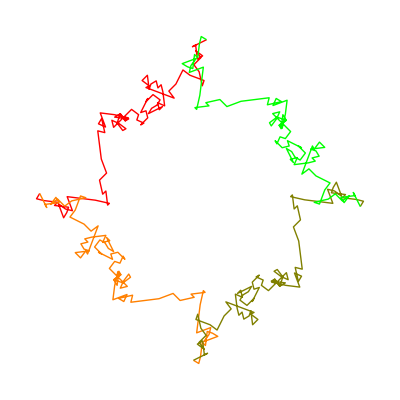

```mathematica
Graphics[{
Red,
Line[ Subscript[m, 0]],
Orange,
Line[mt1],
Darker[Yellow,0.5],
Line[mt2],
Green,
Line[mt3]}]
```